# Evolving on the GPU

With "TargetDevice" -> "GPU", HGEvolvepaclet:WolframInstitute/HypergraphRewriteEngine/ref/HGEvolveWolframInstitute/HypergraphRewriteEngine Package Symbol and HGSessionOpenpaclet:WolframInstitute/HypergraphRewriteEngine/ref/HGSessionOpenWolframInstitute/HypergraphRewriteEngine Package Symbol run on the CUDA engine bundled with the paclet. The GPU engine gives the same states, events and relations as the CPU engine for the same rules, initial states, steps and options.

## Evolving on the GPU

The chain rule and one edge:

```mathematica
rules = {{{1, 2}} -> {{1, 3}, {3, 2}}};
init = {{1, 2}};
Table[HGEvolve[rules, init, k, "NumStates", "TargetDevice" -> "GPU"], {k, 0, 5}]
```

{1,2,4,10,34,154}

The first GPU evaluation starts a worker process that keeps the GPU open for the rest of the Wolfram Language session, and later evaluations and session verbs use the same worker.

## The same results on both devices

The number of states under each "CanonicalizeStates" setting, from the CPU and from the GPU:

```mathematica
rules = {{{1, 2}} -> {{1, 3}, {3, 2}}};
Table[{mode, HGEvolve[rules, {{1, 2}}, 5, "NumStates", "CanonicalizeStates" -> mode], HGEvolve[rules, {{1, 2}}, 5, "NumStates", "CanonicalizeStates" -> mode, "TargetDevice" -> "GPU"]}, {mode, {None, Automatic, Full}}]
```

{{None,154,154},{Automatic,154,154},{Full,6,6}}

A rule from the Wolfram Physics Project:

```mathematica
physics = {{{1, 2}, {1, 3}} -> {{1, 2}, {1, 4}, {2, 4}, {3, 4}}};
physicsInit = {{1, 2}, {1, 3}};
```

The states graph after three steps with isomorphic states merged, from the CPU:

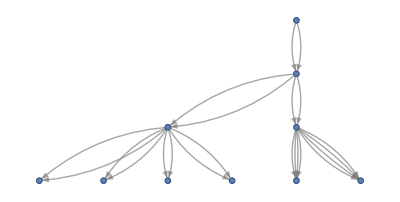

```mathematica
statesCPU = HGEvolve[physics, physicsInit, 3, "StatesGraphStructure", "CanonicalizeStates" -> Full, ImageSize -> 400, AspectRatio -> 1/2]
```

The same graph from the GPU. State ids are assigned separately in each run, so the two graphs are compared by their sizes and out-degrees:

```mathematica
statesGPU = HGEvolve[physics, physicsInit, 3, "StatesGraphStructure", "CanonicalizeStates" -> Full, "TargetDevice" -> "GPU", ImageSize -> 400, AspectRatio -> 1/2]
```

-Graphics-

```mathematica
{Sort[VertexOutDegree[statesCPU]] === Sort[VertexOutDegree[statesGPU]], VertexCount /@ {statesCPU, statesGPU}, EdgeCount /@ {statesCPU, statesGPU}}
```

{True,{10,10},{22,22}}

The four counts at four steps from each device:

```mathematica
Table[Prepend[device] @ Values @ HGEvolve[physics, physicsInit, 4, "Debug", "CanonicalizeStates" -> Full, "TargetDevice" -> device], {device, {"CPU", "GPU"}}]
```

{{CPU,45,126,124,111},{GPU,45,126,124,111}}

With "ExploreFromCanonicalStatesOnly" -> True, each isomorphism class is expanded once, and both devices give the counts of the full exploration:

```mathematica
Table[Prepend[device] @ Values @ HGEvolve[physics, physicsInit, 4, "Debug", "CanonicalizeStates" -> Full, "ExploreFromCanonicalStatesOnly" -> True, "TargetDevice" -> device], {device, {"CPU", "GPU"}}]
```

{{CPU,45,126,124,111},{GPU,45,126,124,111}}

## Sampling on the GPU

"TransitionRate", "RuleWeights", "ExplorationProbability" and "MatchesPerStateRule" decide from each transition's isomorphism-invariant identity and "RandomSeed", so the same seed keeps the same transitions on both devices.

A rule that replaces two adjacent edges by four, from two loops, keeping each transition with probability 0.25:

```mathematica
branching = {{{1, 2}, {2, 3}} -> {{1, 3}, {3, 4}, {1, 4}, {2, 4}}};
Table[Prepend[device] @ Values @ HGEvolve[branching, {{1, 1}, {1, 1}}, 5, "Debug", "TransitionRate" -> 0.25, "RandomSeed" -> 7, "TargetDevice" -> device], {device, {"CPU", "GPU"}}]
```

{{CPU,11,10,9,2},{GPU,11,10,9,2}}

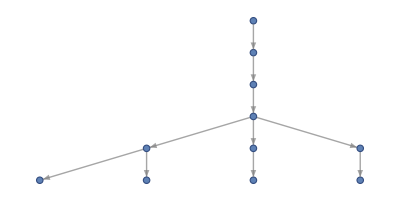

```mathematica
branching = {{{1, 2}, {2, 3}} -> {{1, 3}, {3, 4}, {1, 4}, {2, 4}}};
HGEvolve[branching, {{1, 1}, {1, 1}}, 5, "StatesGraphStructure", "TransitionRate" -> 0.25, "RandomSeed" -> 7, "TargetDevice" -> "GPU", ImageSize -> 400, AspectRatio -> 1/2]
```

The caps, "MaxStatesPerStep", "MaxSuccessorStatesPerParent" and "UniformRandom" with "MatchesPerStep", keep the same transitions as on the CPU.

## A session on the GPU

HGSessionOpenpaclet:WolframInstitute/HypergraphRewriteEngine/ref/HGSessionOpenWolframInstitute/HypergraphRewriteEngine Package Symbol takes "TargetDevice", and the session stays on that device until it is closed:

```mathematica
rules = {{{1, 2}} -> {{1, 3}, {3, 2}}};
session = HGSessionOpen[rules, {{1, 2}}, "NumStates", "TargetDevice" -> "GPU"];
HGSessionStep[session, 2]
```

4

The frontier after two steps:

```mathematica
frontier = Sort[HGSessionFrontier[session]]
```

{2,3}

One step from the last frontier state only:

```mathematica
HGSessionStep[session, 1, "From" -> {Last[frontier]}]
```

7

A step without "From" expands the state left out as well, and the session holds the evolution of four steps:

```mathematica
{HGSessionStep[session, 1], HGEvolve[rules, {{1, 2}}, 4, "NumStates"]}
```

{34,34}

```mathematica
HGSessionClose[session]
```

## Capacity

The GPU engine sizes its memory pools before a run, from the number of steps and the initial state. A pool that fills is enlarged and the run repeated. When a pool cannot be enlarged enough, the run ends early, HGEvolvepaclet:WolframInstitute/HypergraphRewriteEngine/ref/HGEvolveWolframInstitute/HypergraphRewriteEngine Package Symbol issues the message HGEvolve::overflow, and the result is partial. Fewer steps, "CanonicalizeStates" -> Full with "ExploreFromCanonicalStatesOnly" -> True, or the CPU engine avoid it.

## When no GPU engine is available

Where the paclet has no GPU engine for the platform, "TargetDevice" -> "GPU" issues the message HGEvolve::gpudev and the evolution runs on the CPU.

A value other than "CPU" or "GPU" issues HGEvolve::baddev, and the evolution runs on the CPU:

```mathematica
HGEvolve[{{{1, 2}} -> {{1, 3}, {3, 2}}}, {{1, 2}}, 3, "NumStates", "TargetDevice" -> "TPU"]
```

HGEvolve::baddev: TargetDevice -> TPU is not valid; use CPU or GPU. Using CPU.

10

Related Guides

HypergraphRewritingpaclet:WolframInstitute/HypergraphRewriteEngine/guide/HypergraphRewriting

Related Tech Notes

GettingStartedpaclet:WolframInstitute/HypergraphRewriteEngine/tutorial/GettingStarted ▪ SamplingAndPruningpaclet:WolframInstitute/HypergraphRewriteEngine/tutorial/SamplingAndPruning ▪ Sessionspaclet:WolframInstitute/HypergraphRewriteEngine/tutorial/Sessions

## Metadata

### Categorization

Tutorial

WolframInstitute/HypergraphRewriteEngine

HypergraphRewriting`

WolframInstitute/HypergraphRewriteEngine/tutorial/GPUEvolution

### Keywords

GPU

CUDA

TargetDevice

hypergraph

multiway

rewriting

parity

session

Wolfram physics